```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/cq/1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/cq/Poluprovodnikovy_lazer.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/cq/~$1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/cq/~$Poluprovodnikovy_lazer.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/cq/1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

## Dataset 1

```mathematica
datasetred = makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
datared = raw⟦2⟧⟦2;;⟧
```

{{2.643,43.15},{2.608,41.53},{2.555,38.56},{2.521,36.59},{2.507,35.59},{2.489,34.58},{2.468,33.57},{2.45,32.61},{2.432,31.61},{2.415,30.6},{2.397,29.59},{2.38,28.64},{2.363,27.63},{2.345,26.62},{2.326,25.61},{2.31,24.66},{2.291,23.64},{2.271,22.63},{2.254,21.62},{2.236,20.61},{2.218,19.66},{2.2,18.65},{2.182,17.64},{2.164,16.63},{2.146,15.68},{2.129,14.67},{2.109,13.66},{2.09,12.65},{2.071,11.69},{2.052,10.68},{2.032,9.67},{2.012,8.66},{1.994,7.71},{1.971,6.69},{1.948,5.68},{1.926,4.68},{1.903,3.72},{1.875,2.71},{1.842,1.7},{1.796,0.69}}

```mathematica
dataredline=Normal[NonlinearModelFit[datared,a(Exp[b x]-1)+c,{a,b,c},x]]
```

-57.1105+51.3895 (-1+ⅇ^(0.411525 x))

## Dataset 2

```mathematica
datasetyellow = makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
datayellow = raw⟦3⟧⟦2;;⟧
```

{{2.596,41.25},{2.568,39.73},{2.551,38.71},{2.534,37.7},{2.517,36.75},{2.501,35.73},{2.484,34.73},{2.466,33.72},{2.449,32.76},{2.433,31.75},{2.416,30.74},{2.4,29.73},{2.384,28.78},{2.367,27.76},{2.351,26.75},{2.334,25.74},{2.318,24.78},{2.302,23.77},{2.284,22.76},{2.266,21.75},{2.249,20.74},{2.233,19.78},{2.215,18.77},{2.198,17.76},{2.18,16.75},{2.162,15.8},{2.143,14.78},{2.125,13.77},{2.106,12.76},{2.087,11.81},{2.068,10.8},{2.047,9.78},{2.027,8.78},{2.006,7.82},{1.983,6.81},{1.959,5.8},{1.934,4.79},{1.907,3.83},{1.876,2.82},{1.837,1.81},{1.78,0.8}}

```mathematica
datayellowline=Normal[NonlinearModelFit[datayellow,a(Exp[b x]-1)+c,{a,b,c},x]]
```

-38.7435+13.3957 (-1+ⅇ^(0.752038 x))

## Dataset 3

```mathematica
datasetgreen = makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
datagreen = raw⟦4⟧⟦2;;⟧
```

{{2.598,35.72},{2.583,34.884},{2.562,33.81},{2.545,32.84},{2.525,31.82},{2.506,30.81},{2.486,29.8},{2.469,28.84},{2.449,27.83},{2.432,26.81},{2.412,25.8},{2.395,24.84},{2.375,23.83},{2.357,22.82},{2.337,21.8},{2.318,20.79},{2.306,19.83},{2.282,18.82},{2.262,17.82},{2.241,16.81},{2.222,15.85},{2.204,14.84},{2.183,13.82},{2.161,12.81},{2.155,11.86},{2.134,10.85},{2.108,9.83},{2.084,8.82},{2.061,7.86},{2.034,6.85},{2.009,5.85},{1.979,4.83},{1.952,3.87},{1.921,2.87},{1.879,1.86},{1.823,0.84}}

```mathematica
datagreenline=Normal[NonlinearModelFit[datagreen,a(Exp[b x]-1)+c,{a,b,c},x]]
```

-34.8755+11.1452 (-1+ⅇ^(0.770027 x))

## Dataset 4

```mathematica
datasetblue = makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
datablue = raw⟦5⟧⟦2;;⟧
```

{{2.648,0.349},{2.643,0.325},{2.64,0.313},{2.635,0.289},{2.63,0.27},{2.625,0.252},{2.62,0.235},{2.615,0.218},{2.61,0.2},{2.605,0.188},{2.6,0.175},{2.595,0.161},{2.59,0.149},{2.585,0.138},{2.58,0.128},{2.575,0.118},{2.57,0.109},{2.565,0.1},{2.56,0.094},{2.55,0.078},{2.545,0.073},{2.54,0.065},{2.535,0.06},{2.53,0.054},{2.525,0.05},{2.52,0.045},{2.515,0.041},{2.51,0.037},{2.505,0.034},{2.5,0.031},{2.49,0.025},{2.485,0.022},{2.48,0.021},{2.475,0.018},{2.47,0.016},{2.465,0.014},{2.46,0.013},{2.455,0.012},{2.45,0.01},{2.445,0.009},{2.44,0.008},{2.435,0.007},{2.43,0.006},{2.4,0.003},{2.41,0.004},{2.389,0.002},{2.37,0.0015},{2.36,0.0012},{2.35,0.0009},{2.34,0.0006},{2.33,0.0004},{2.32,0.0003},{2.311,0.0002},{2.301,0.0001}}

```mathematica
datablueline=Normal[NonlinearModelFit[datablue,a+c(Exp[b x]),{a,b,c},x]]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-0.393653+0.00341347 ⅇ^(1.96702 x)

## Dataset 5

```mathematica
datasetwhite = makeDataset[raw⟦6⟧]
```

Dataset[<>]

```mathematica
datawhite = raw⟦6⟧⟦2;;⟧
```

{{2.649,0.812},{2.645,0.762},{2.64,0.702},{2.635,0.645},{2.63,0.588},{2.625,0.536},{2.62,0.489},{2.615,0.443},{2.61,0.4},{2.605,0.359},{2.6,0.324},{2.595,0.29},{2.59,0.259},{2.585,0.23},{2.58,0.204},{2.575,0.181},{2.57,0.159},{2.565,0.139},{2.56,0.123},{2.555,0.108},{2.55,0.094},{2.545,0.082},{2.54,0.071},{2.535,0.062},{2.53,0.054},{2.525,0.047},{2.52,0.042},{2.515,0.036},{2.51,0.031},{2.505,0.027},{2.5,0.023},{2.495,0.02},{2.49,0.0172},{2.485,0.015},{2.48,0.0133},{2.475,0.0112},{2.47,0.0096},{2.465,0.0087},{2.46,0.0075},{2.455,0.0063},{2.45,0.0057},{2.445,0.0047},{2.44,0.0041},{2.435,0.0037},{2.425,0.0027},{2.415,0.002},{2.405,0.0015},{2.395,0.0012},{2.38,0.0007},{2.365,0.0005},{2.35,0.0002},{2.335,0.0001}}

```mathematica
datawhiteline=Normal[NonlinearModelFit[datawhite,a+c Exp[b x],{a,b,c},x]]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

12.2961-18.9867 ⅇ^(-0.177849 x)

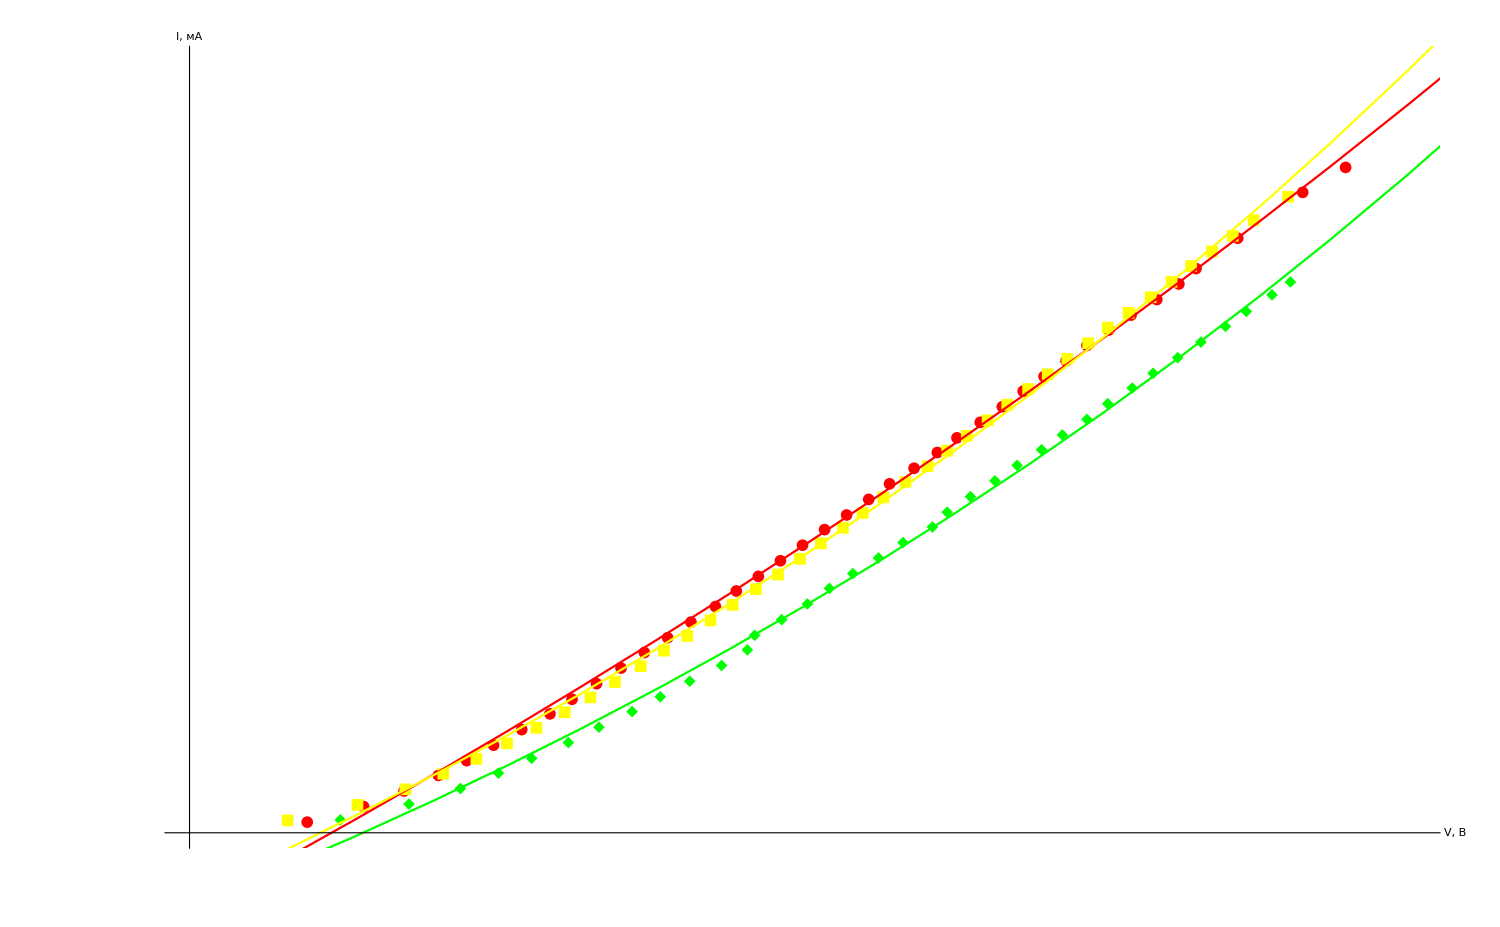

```mathematica
Show[
ListPlot[
{datasetred,datasetyellow,datasetgreen},
PlotRange-> {{1.7,2.7},{0, 50}},
Ticks-> {Range[-1000,1000, 0.2],Range[-1000,1000, 2]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
PlotStyle->{Red,Yellow,Green},
AxesLabel-> {Style["V, В", Large], Style["I, мА", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.025],Range[-1000,1000, 1]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
{},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.6],Scaled[0.75]}
]
],
Plot[{dataredline,datayellowline,datagreenline},{x,0, 3},PlotStyle->{Red,Yellow,Green}]
]
```

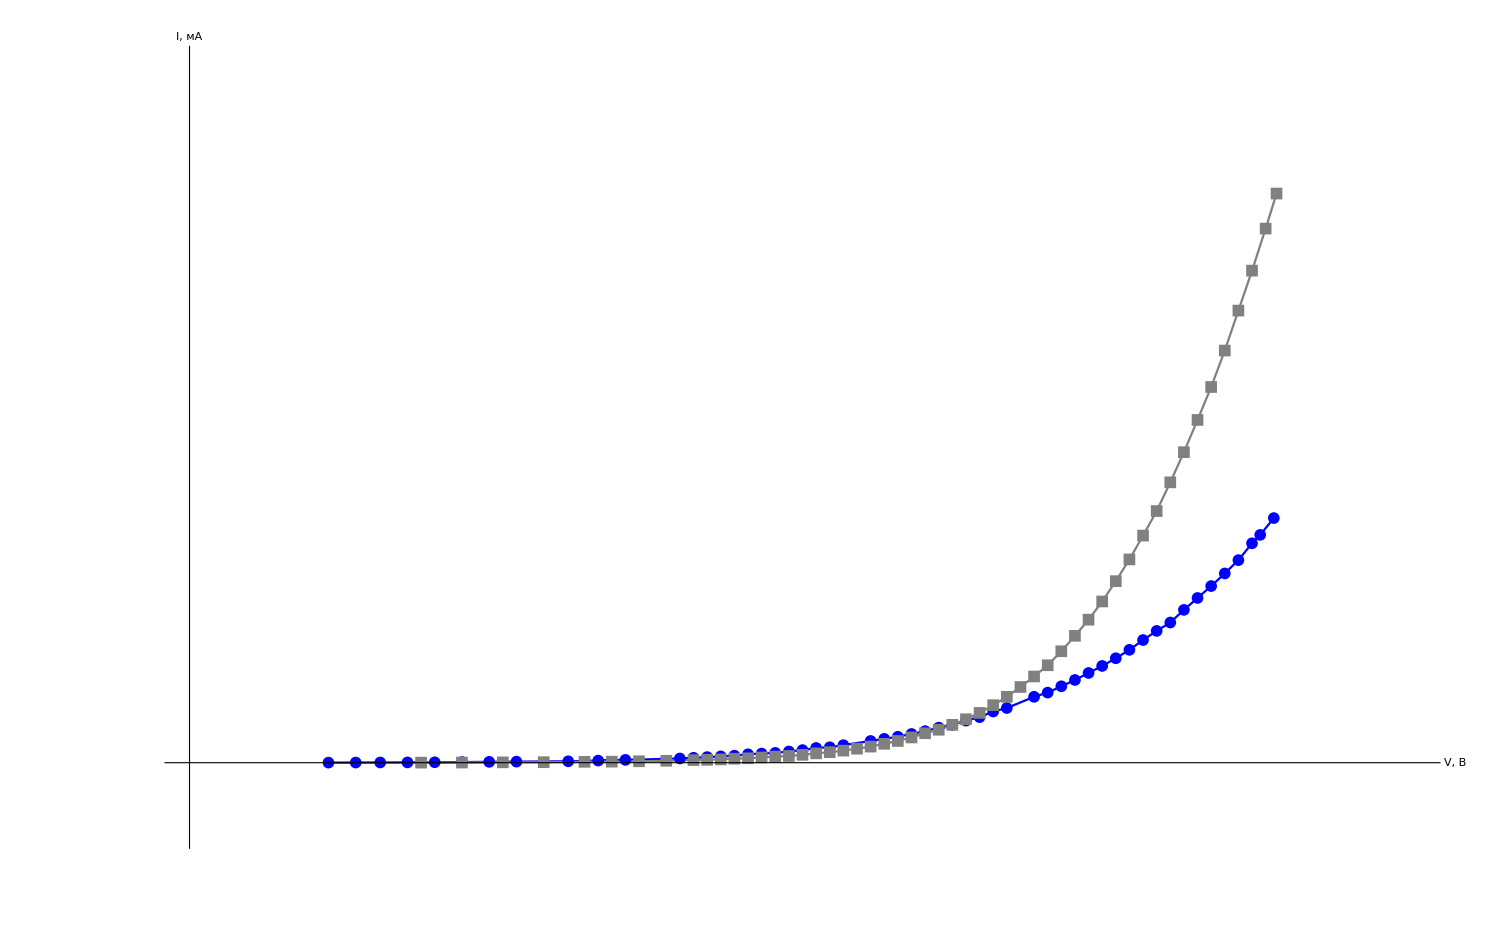

```mathematica
Show[
ListPlot[
{datasetblue,datasetwhite},
PlotRange-> {{2.25,2.7},{-0.1, 1}},
Ticks-> {Range[-1000,1000, 0.2],Range[-1000,1000, 0.1]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
PlotStyle->{Blue, Gray},
AxesLabel-> {Style["V, В", Large], Style["I, мА", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.0125],Range[-1000,1000, 0.025]},
LabelStyle->Black,
Joined->True,
PlotLegends->Placed[LineLegend[
{},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.6],Scaled[0.75]}
]
](*,
Plot[{datablueline,datawhiteline},{x,0, 3}]*)
]
```

## Dataset 8

```mathematica
datasetreddiod = makeDataset[raw⟦8⟧]
```

Dataset[<>]

```mathematica
datasetreddiod = raw⟦8⟧⟦2;;⟧
```

{{554.,0.082},{555.,0.0825},{556.,0.083},{557.,0.0825},{558.,0.0825},{559.,0.081},{560.,0.082},{561.,0.082},{562.,0.0805},{563.,0.0815},{564.,0.0805},{565.,0.0825},{566.,0.0815},{567.,0.0825},{568.,0.082},{569.,0.08},{570.,0.083},{571.,0.083},{572.,0.082},{573.,0.0815},{574.,0.082},{575.,0.082},{576.,0.083},{577.,0.0825},{578.,0.0835},{579.,0.0865},{580.,0.083},{581.,0.0855},{582.,0.0865},{583.,0.0875},{584.,0.0885},{585.,0.0865},{586.,0.0875},{587.,0.088},{588.,0.089},{589.,0.089},{590.,0.092},{591.,0.0935},{592.,0.0965},{593.,0.0975},{594.,0.102},{595.,0.104},{596.,0.1045},{597.,0.11},{598.,0.113},{599.,0.121},{600.,0.125},{601.,0.1285},{602.,0.1355},{603.,0.142},{604.,0.1515},{605.,0.159},{606.,0.1665},{607.,0.173},{608.,0.189},{609.,0.199},{610.,0.2095},{611.,0.224},{612.,0.2375},{613.,0.2505},{614.,0.2665},{615.,0.28},{616.,0.299},{617.,0.3155},{618.,0.334},{619.,0.354},{620.,0.3785},{621.,0.399},{622.,0.418},{623.,0.447},{624.,0.4705},{625.,0.4975},{626.,0.5205},{627.,0.551},{628.,0.5845},{629.,0.6115},{630.,0.6425},{631.,0.678},{632.,0.7065},{633.,0.746},{634.,0.7705},{635.,0.8165},{636.,0.848},{637.,0.89},{638.,0.925},{639.,0.9705},{640.,1.0045},{641.,1.0465},{642.,1.0905},{643.,1.1285},{644.,1.1775},{645.,1.215},{646.,1.2505},{647.,1.2895},{648.,1.342},{649.,1.3775},{650.,1.4255},{651.,1.461},{652.,1.5285},{653.,1.549},{654.,1.6005},{655.,1.641},{656.,1.6795},{657.,1.7235},{658.,1.7745},{659.,1.791},{660.,1.8355},{661.,1.883},{662.,1.923},{663.,1.954},{664.,1.9885},{665.,2.0315},{666.,2.0655},{667.,2.0805},{668.,2.114},{669.,2.159},{670.,2.1785},{671.,2.208},{672.,2.2165},{673.,2.235},{674.,2.276},{675.,2.2945},{676.,2.312},{677.,2.3265},{678.,2.334},{679.,2.3525},{680.,2.3465},{681.,2.3695},{682.,2.357},{683.,2.3675},{684.,2.362},{685.,2.3695},{686.,2.3465},{687.,2.34},{688.,2.338},{689.,2.3155},{690.,2.3155},{691.,2.3165},{692.,2.289},{693.,2.27},{694.,2.251},{695.,2.217},{696.,2.1995},{697.,2.1745},{698.,2.158},{699.,2.1105},{700.,2.0915},{701.,2.059},{702.,2.0295},{703.,1.999},{704.,1.962},{705.,1.9325},{706.,1.8815},{707.,1.851},{708.,1.831},{709.,1.7915},{710.,1.76},{711.,1.7205},{712.,1.6765},{713.,1.6335},{714.,1.598},{715.,1.565},{716.,1.535},{717.,1.4845},{718.,1.4515},{719.,1.412},{720.,1.376},{721.,1.3485},{722.,1.3035},{723.,1.267},{724.,1.2345},{725.,1.205},{726.,1.1705},{727.,1.134},{728.,1.0875},{729.,1.06},{730.,1.039},{731.,0.9985},{732.,0.9745},{733.,0.9475},{734.,0.923},{735.,0.883},{736.,0.8575},{737.,0.8285},{738.,0.799},{739.,0.78},{740.,0.752},{741.,0.7315},{742.,0.709},{743.,0.681},{744.,0.6555},{745.,0.6395},{746.,0.617},{747.,0.595},{748.,0.573},{749.,0.559},{750.,0.541},{751.,0.523},{752.,0.5085},{753.,0.4835},{754.,0.4725},{755.,0.455},{756.,0.439},{757.,0.418},{758.,0.413},{759.,0.3985},{760.,0.385},{761.,0.37},{762.,0.3555},{763.,0.345},{764.,0.331},{765.,0.325},{766.,0.3135},{767.,0.301},{768.,0.293},{769.,0.285},{770.,0.2745},{771.,0.266},{772.,0.2585},{773.,0.2575},{774.,0.2445},{775.,0.2415},{776.,0.23},{777.,0.2255},{778.,0.2175},{779.,0.2085},{780.,0.2065},{781.,0.1985},{782.,0.195},{783.,0.19},{784.,0.184},{785.,0.182},{786.,0.1735},{787.,0.171},{788.,0.1625},{789.,0.163},{790.,0.158},{791.,0.156},{792.,0.1535},{793.,0.15},{794.,0.147},{795.,0.1435},{796.,0.1375},{797.,0.138},{798.,0.1365},{799.,0.13},{800.,0.128},{801.,0.127},{802.,0.126},{803.,0.1195},{804.,0.122},{805.,0.116},{806.,0.117},{807.,0.117},{808.,0.112},{809.,0.112},{810.,0.1115},{811.,0.109},{812.,0.108},{813.,0.1055},{814.,0.1045},{815.,0.101},{816.,0.101},{817.,0.1015},{818.,0.1005},{819.,0.1005},{820.,0.0975},{821.,0.096},{822.,0.0965},{823.,0.0945},{824.,0.0955},{825.,0.094},{826.,0.0935},{827.,0.0945},{828.,0.0945},{829.,0.0915},{830.,0.0925},{831.,0.091},{832.,0.0905},{833.,0.089},{834.,0.09},{835.,0.089},{836.,0.09},{837.,0.088},{838.,0.087},{839.,0.088},{840.,0.087},{841.,0.0865},{842.,0.0855},{843.,0.086},{844.,0.0855},{845.,0.0855},{846.,0.085},{847.,0.084},{848.,0.085},{849.,0.0865},{850.,0.084}}

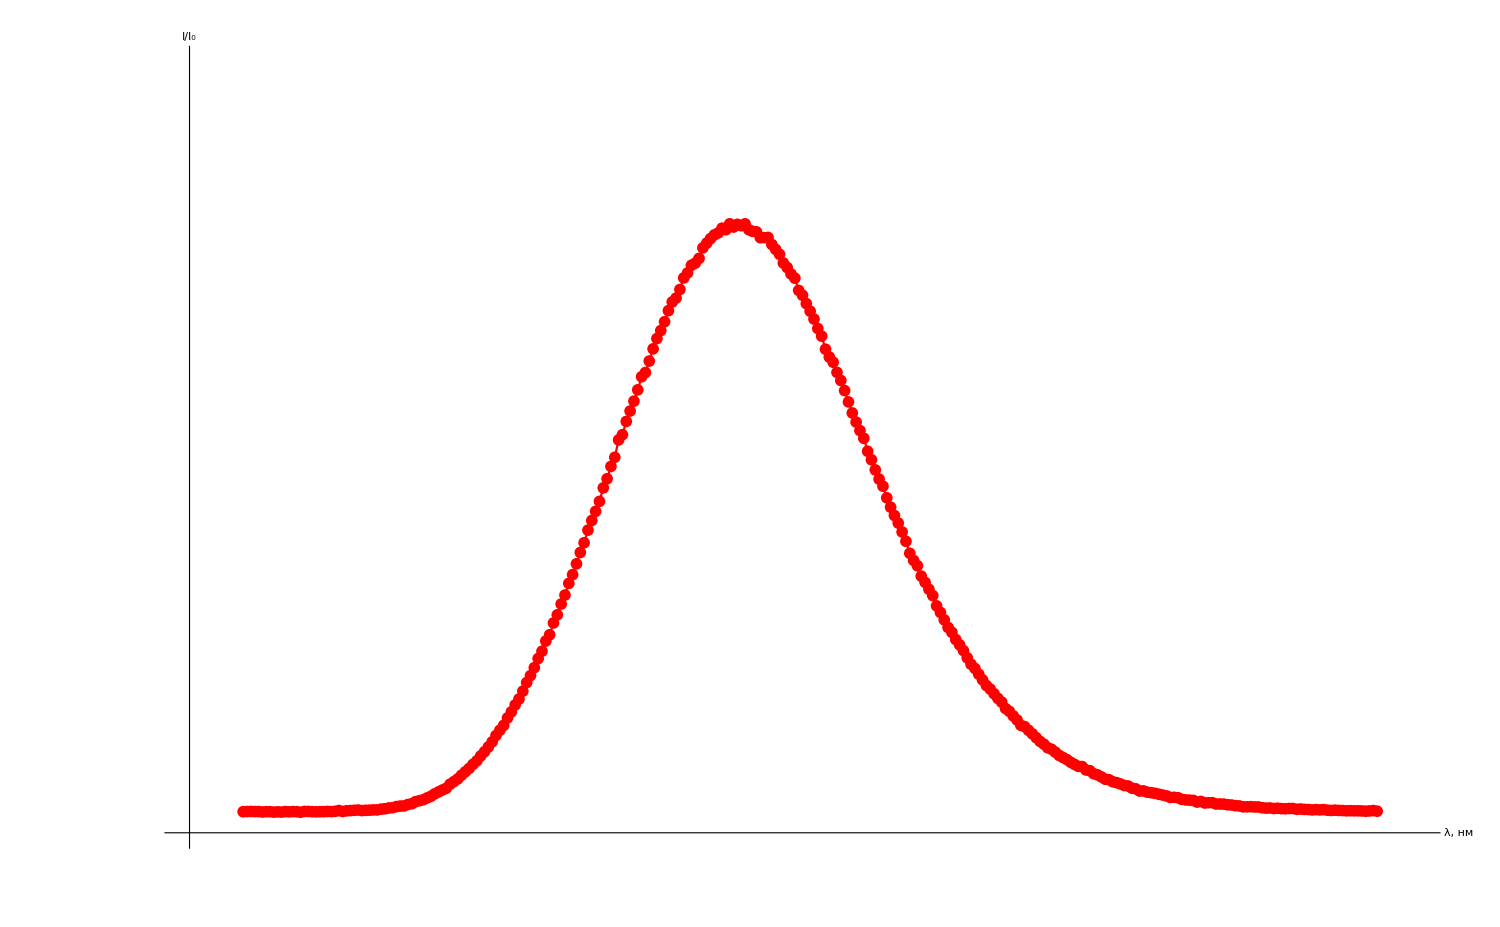

```mathematica
Show[
ListPlot[
{datasetreddiod},
PlotRange-> {{540,860},{0, 3}},
Ticks-> {Range[-1000,1000, 10],Range[-1000,1000, 0.1]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
PlotStyle->{Red},
AxesLabel-> {Style["λ, нм", Large], Style["I/I_0", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 10],Range[-1000,1000, 0.1]},
LabelStyle->Black,
Joined->True,
PlotLegends->Placed[LineLegend[
{},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.6],Scaled[0.75]}
]
]
]
```

## Dataset 9

```mathematica
dataselaserdiod = makeDataset[raw⟦9⟧]
```

Dataset[<>]

```mathematica
datasetlaserdiod = raw⟦9⟧⟦2;;⟧;
```

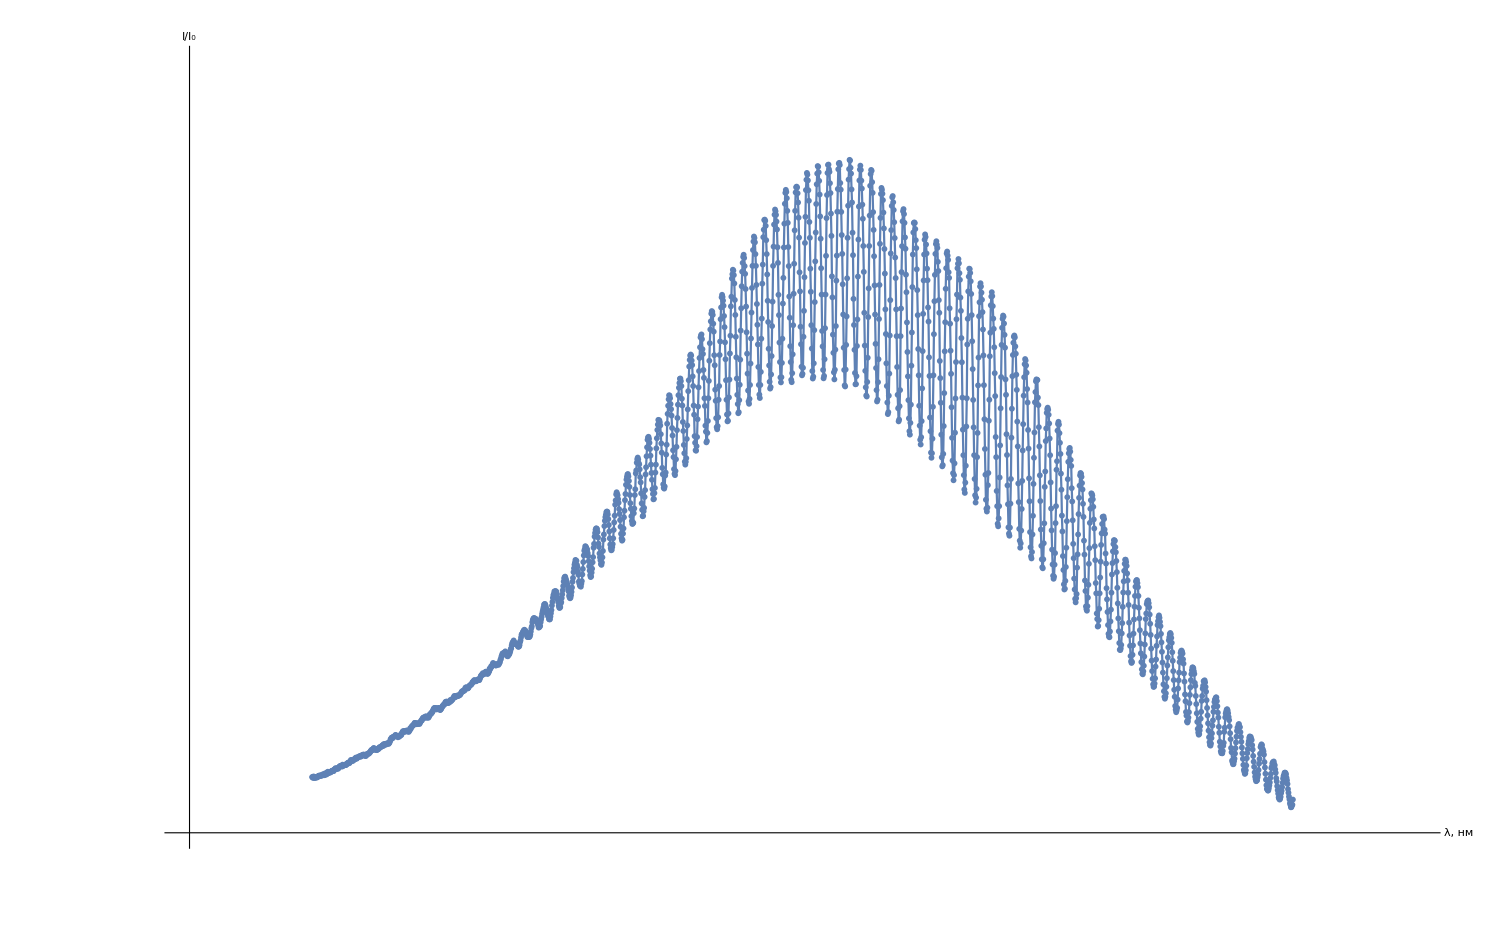

```mathematica
Show[
ListPlot[
{datasetlaserdiod},
PlotRange-> {{815,865},{0.2, 2}},
Ticks-> {Range[-1000,1000, 5],Range[-1000,1000, 0.1]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 6},
AxesLabel-> {Style["λ, нм", Large], Style["I/I_0", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 1.25],Range[-1000,1000, 0.05]},
LabelStyle->Black,
Joined->True,
PlotLegends->Placed[LineLegend[
{},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.6],Scaled[0.75]}
]
]
]
```